```mathematica
RatioPenalty[x_,y_,u_,v_]:=1+u/x+v/y(*(x/y-u/v)+(y/x-v/u)*)
```

```mathematica
Plot3D[{
RatioPenalty[x,y,1,1],
RatioPenalty[x,y,0.1,0.5]
},{x,0,1},{y,0,1},
PlotRange->{0,10},
ClippingStyle->None,
PlotPoints->50,
PlotStyle->{Yellow,Blue}]
```

-Graphics3D-

```mathematica
f[x_]:= Norm[x]
D[f[x]^2,x]
```

2 Norm[x] Norm'[x]

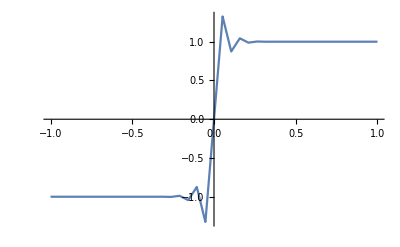

```mathematica
Plot[ Norm'[x],{x,-1,1}]
```

```mathematica
fun[x_,y_]:=(x-0.5)^2*(0.5-y)^2
Plot3D[{fun[x,y],0},{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Minimize[Norm[{x,y}-{1,1}],(x-0.5)*(y-0.49)==0,{x,y}]
```

{0.5,{x→0.5,y→0.999942}}

```mathematica
Grad[(x-0.5)^2*(0.5-y)^2,{x,y}]
```

{2 (-0.5+x) (0.5-y)^2,-2 (-0.5+x)^2 (0.5-y)}